```mathematica
Pmul[n_,bigN_,Ph_]:=∑_(i=n)^∞ Binomial[bigN,i] Ph^i(1-Ph)^(bigN-i)
```

```mathematica
DiscretePlot3D[Pmul[n,bigN,0.1],{n,1,10},{bigN,1,50},ExtentSize->Full,AxesLabel->{"n"," N","P_(≥n) "},BaseStyle->{FontSize->15},PlotLabel->"χ=0.1"]
```

-Graphics3D-

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Pss[n_,χ_]:=Binomial[n^2,n] χ^(2n)(1-χ^2)^(n^2)
```

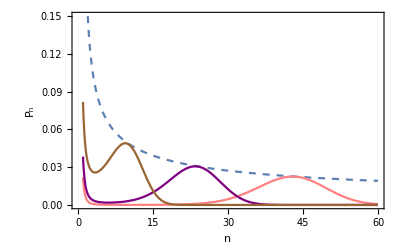

```mathematica
Plot[{1/(ⅇ √(2π(n-1))),Pss[n,0.15],Pss[n,0.2],Pss[n,0.3]},{n,1,60},Frame->True,BaseStyle->{FontSize->15},PlotRange->{0,0.15}, FrameLabel->{"n","P_n"},PlotLegend->{"max","χ=0.15","χ=0.2","χ=0.3"},LegendShadow->False,LegendPosition->{0.35,0.05},PlotStyle->{Dashed,Pink,Purple,Brown},LegendSize->{0.5,0.5}]
```